# Quantum rotor F=1

```mathematica
ClearAll["`*"];
ClearAll["Global`*"];
```

## Parameters

```mathematica
sizex=1;(* sizex=1 *)
xr=0.5 sizex;
yr=xr;
α0=4000;
α1=8000;
E0=0.5;
I1=1.5
```

1.5

```mathematica
Fx=1/(√2){{0,1,0},{1,0,1},{0,1,0}};
Fy=1/(√2){{0,-ⅈ,0},{ⅈ,0,-ⅈ},{0,ⅈ,0}};
Fz={{1,0,0},{0,0,0},{0,0,-1}};
Fr=1/(√2){{0,(x-ⅈ y)/Sqrt[x^2+y^2],0},{(x+ⅈ y)/Sqrt[x^2+y^2],0,(x-ⅈ y)/Sqrt[x^2+y^2]},{0,(x+ⅈ y)/Sqrt[x^2+y^2],0}};
```

```mathematica
{((Fx.Fy-Fy.Fx)-ⅈ Fz)//MatrixForm, ((Fy.Fz-Fz.Fy)-ⅈ Fx)//MatrixForm, ((Fz.Fx-Fx.Fz)-ⅈ Fy)//MatrixForm}
```

{(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)}

## Derivation of V and B (anisotropic)

```mathematica
setangle[angle_] :=Module[{degs,q,xyrotation,rs},
degs = {0, angle, Pi, Pi+angle};
rs = {xr,yr,xr,yr};
currentAngle = angle;
beta=1/Sqrt[2];
xyrotation= RotationMatrix[angle/2, {0,0,1}];
q[deg_] := {Cos[deg], Sin[deg], 0}; 
Evec[x_, y_, z_]:=Inverse[xyrotation].Sum[(Sqrt[1-beta^2]{0, 0, 1}+beta Cross[q[degs[[i]]], {0,0,1}])Exp[2Pi I /(2*rs[[i]])*q[degs[[i]]].xyrotation.{x,y,z}], {i,1,4}]; (*dodac /(2*rs[[i]])?*)


nxr = xr/(2Cos[angle/2]);
nyr = yr/(2Sin[angle/2]);
vscalar[x_, y_]:=(-((α0 E0^2)/4))*Conjugate[Evec[x, y, 0]] . Evec[x, y, 0];
bvector[x_, y_]:=(-((I α1 E0^2)/(4*(2*I1 + 1))))*Cross[Conjugate[Evec[x, y, 0]], Evec[x, y, 0]];
V=vscalar[x,y] (* LICZY SIĘ!*);
{Bx,By,zero}=bvector[x,y];]
```

```mathematica
ANGLE =90*Pi/180;
setangle[ANGLE]
```

## Solving the equations

### Bulk states

```mathematica
Remove[fsol]
```

```mathematica
{xn,yn}={2,2};(* supercell size n x m (e.g. 2x2 )*)

fsol[B_,kx_,ky_,a_:1,b_:1,shift_, numi_ : 12]:=(*fsol[B,kx,ky,a,b,shift, numi]=*)NDEigensystem[{
({
-1/2 Laplacian[ψ1[x,y] Exp[2 Pi I kx x/(2 xn nxr)] Exp[2 Pi I ky y/(2 yn nyr)],{x,y}] Exp[-2 Pi I kx x/(2 xn nxr)] Exp[-2 Pi I ky y/(2 yn nyr)],
-1/2 Laplacian[ψ2[x,y] Exp[2 Pi I kx x/(2 xn nxr)] Exp[2 Pi I ky y/(2 yn nyr)],{x,y}] Exp[-2 Pi I kx x/(2 xn nxr)] Exp[-2 Pi I ky y/(2 yn nyr)],
-1/2 Laplacian[ψ3[x,y] Exp[2 Pi I kx x/(2 xn nxr)] Exp[2 Pi I ky y/(2 yn nyr)],{x,y}] Exp[-2 Pi I kx x/(2 xn nxr)] Exp[-2 Pi I ky y/(2 yn nyr)]
}
+(a^2 (IdentityMatrix[3] V-b Bx Fx-b By Fy)-B Fz).{ψ1[x,y],ψ2[x,y],ψ3[x,y]}),

PeriodicBoundaryCondition[{ψ1[x,y],ψ2[x,y], ψ3[x,y]},(-nxr<=x<=(2 xn-1) nxr)&&(y==-nyr),(#+2 yn nyr {0,1})&],
PeriodicBoundaryCondition[{ψ1[x,y],ψ2[x,y], ψ3[x,y]},(-nyr<=y<=(2 yn-1) nyr)&&(x==-nxr),(#+2 xn nxr {1,0})&]},{ψ1,ψ2, ψ3},{x,-nxr,+(2 xn-1) nxr},{y,-nyr,+(2 yn-1) nyr},
numi, (*number of states calculated*)
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.002}}},"Eigensystem"->{"Arnoldi","Shift"->shift,"Criteria"->"RealPart","BasisSize" -> 60,MaxIterations->10000}}];
```

### Strip with Dirichlet boundary conditions at y = ± y_max

```mathematica
Remove[fEsol]
```

```mathematica
(*{xn}={1};*)
fEsol[B_,kx_,yn_Integer,a_:1,b_:1,shift_]:=fEsol[B,kx,yn,a,b,shift]=NDEigensystem[{
({
-1/2 Laplacian[ψ1[x,y] Exp[2 Pi I kx x/(2 xn nxr)],{x,y}] Exp[-2 Pi I kx x/(2 xn nxr)],
-1/2 Laplacian[ψ2[x,y] Exp[2 Pi I kx x/(2 xn nxr)],{x,y}] Exp[-2 Pi I kx x/(2 xn nxr)],
-1/2 Laplacian[ψ3[x,y] Exp[2 Pi I kx x/(2 xn nxr)],{x,y}] Exp[-2 Pi I kx x/(2 xn nxr)]
}
+(a^2 (IdentityMatrix[3] V-b Bx Fx-b By Fy)-B Fz).{ψ1[x,y],ψ2[x,y], ψ3[x,y]}),
PeriodicBoundaryCondition[{ψ1[x,y],ψ2[x,y], ψ3[x,y]},(-nyr<=y<=(2 yn-1) nyr)&&(x==-nxr),(#+2 xn nxr {1,0})&],
DirichletCondition[{ψ1[x,y]==0,ψ2[x,y]==0, ψ3[x,y] == 0},(y==-nyr)&&(-nxr<x<nxr)],
DirichletCondition[{ψ1[x,y]==0,ψ2[x,y]==0, ψ3[x,y] == 0},(y==+(2 yn-1) nyr)&&(-nxr<x<nxr)]},
{ψ1,ψ2, ψ3},{x,-nxr,+nxr},{y,-nyr,+(2 yn-1) nyr},
9 yn,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}},"Eigensystem"->{"Arnoldi","Shift"->shift,"Criteria"->"RealPart",MaxIterations->10000}}];
```

Boundary conditions at x = +- nxr

```mathematica
Remove[fEsol2]
```

```mathematica
(*{yn}={1};*)
fEsol2[B_,ky_,xn_Integer,a_:1,b_:1,shift_]:=fEsol2[B,ky,xn,a,b,shift]=NDEigensystem[{
({
-1/2 Laplacian[ψ1[x,y] Exp[2 Pi I ky y/(2 yn nyr)],{x,y}] Exp[-2 Pi I ky y/(2 yn nyr)],
-1/2 Laplacian[ψ2[x,y] Exp[2 Pi I ky y/(2 yn nyr)],{x,y}] Exp[-2 Pi I ky y/(2 yn nyr)],
-1/2 Laplacian[ψ3[x,y] Exp[2 Pi I ky y/(2 yn nyr)],{x,y}] Exp[-2 Pi I ky y/(2 yn nyr)]
}
+(a^2 (IdentityMatrix[3] V-b Bx Fx-b By Fy)-B Fz).{ψ1[x,y],ψ2[x,y], ψ3[x,y]}),

PeriodicBoundaryCondition[{ψ1[x,y],ψ2[x,y], ψ3[x,y]},(-nxr<=x<=(2 xn-1) nxr)&&(y==-nyr),(#+2 yn nyr {1,0})&],
DirichletCondition[{ψ1[x,y]==0,ψ2[x,y]==0, ψ3[x,y] == 0},(x==-nxr)&&(-nyr<y<nyr)],
DirichletCondition[{ψ1[x,y]==0,ψ2[x,y]==0, ψ3[x,y] == 0},(x==+(2 xn-1) nxr)&&(-nyr<y<nyr)]},
{ψ1,ψ2, ψ3},{y,-nyr,+nyr},{x,-nxr,+(2 xn-1) nxr},
9 xn,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}},"Eigensystem"->{"Arnoldi","Shift"->shift,"Criteria"->"RealPart",MaxIterations->10000}}];
```

### Rectangle with Dirichlet bound conditions at x = ± x_max and y = ± y_max

```mathematica
Remove[fEEsol]
fEEsol[B_,{xn_Integer,yn_Integer},a_:1,b_:1,shift_,numi_:3*xn*yn]:=(*fEEsol[B,{xn,yn},a,b,shift]=*) NDEigensystem[{
({
-1/2 Laplacian[ψ1[x,y],{x,y}],
-1/2 Laplacian[ψ2[x,y],{x,y}],
-1/2 Laplacian[ψ3[x,y],{x,y}]
}
+(a^2 (IdentityMatrix[3] V-b Bx Fx-b By Fy)-B Fz).{ψ1[x,y],ψ2[x,y], ψ3[x,y]}),
DirichletCondition[{ψ1[x,y]==0,ψ2[x,y]==0, ψ3[x, y] == 0},True]},
{ψ1,ψ2, ψ3},{x,-nxr,+(2 xn-1) nxr},{y,-nyr,+(2 yn-1) nyr},
numi,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.002}}},"Eigensystem"->{"Arnoldi","Shift"->shift,"Criteria"->"RealPart",MaxIterations->10000}}];
```

```mathematica
nxr
nyr
```

0.353553

0.353553

```mathematica
GuessShift[B_,a_] := -1.1B- 3200*a^2-200
```

```mathematica
Remove[estimateY]
Remove[PlotEnergyFromParameter]
estimateY[y1_,y2_,dx1_,dx2_]:=y2+(y2-y1)/(dx1)*dx2
PlotEnergyFromParameter[d_,join_ : True] := Module[{data, dx1, dx2, i, x, ys,plotted,sortedIndices},
data = d;
Do[
dx1 = data[[i-1,1]]-data[[i-2,1]];
dx2 =data[[i,1]]-data[[i-1,1]];
sortedIndices=Ordering[estimateY[data[[i-2, 2]],data[[i-1,2]],dx1,dx2]];
data[[i,2]][[sortedIndices]]= data[[i,2]],
{i,4,Length[data]}];
x = First[Transpose[data]];
ys = Transpose[Last[Transpose[data]]];
plotted=ListPlot[Table[Transpose[{x, ys[[i]]}],{i, Length[ys]}], Joined->join, InterpolationOrder->1, PlotRange->All];
Return[plotted]]
```

```mathematica
Remove[crossingB]
crossingB[d_] := Module[{data, dx1, dx2, i, xs, ys, f1, f2, r,intersections, sortedIndices},
data = d;
Do[
dx1 = data[[i-1,1]]-data[[i-2,1]];
dx2 =data[[i,1]]-data[[i-1,1]];
sortedIndices=Ordering[estimateY[data[[i-2, 2]],data[[i-1,2]],dx1,dx2]];
data[[i,2]][[sortedIndices]]= data[[i,2]],
{i,4,Length[data]}];
xs = First[Transpose[data]];
ys = Transpose[Last[Transpose[data]]];
f1=Interpolation[Transpose[{xs,ys[[1]]}],InterpolationOrder->3];
f2=Interpolation[Transpose[{xs,ys[[2]]}],InterpolationOrder->3];
(*intersections=x/. NSolve[f1[x]==f2[x],{x,First[xs], Last[xs]}];
r = Min[intersections]; But assuming only one root we can simply write:*)
r = x /.FindRoot[f1[x]-f2[x],{x,First[xs],Last[xs]}];
(*Show[ListPlot[Table[Transpose[{xs, ys[[i]]}],{i, Length[ys]}], Joined->False, InterpolationOrder->1, PlotRange->All]];*)
Return[r]]
```

```mathematica
Remove[EnergyDelta]
EnergyDelta[B_,a_:0.3,b_:2,shift_:-1500] := Module[{d}, d=Chop[First[fsol[B,0,0,a,b,shift, 2]]]; Return[Abs[d[[1]] - d[[2]]]]]
```

```mathematica
Remove[EnDeMin]
EnDeMin[B_,a_:0.3,b_:2,shift_:-1500] := Module[{d}, d=Sort[Chop[First[fsol[B,0,0,a,b,shift, 2]]]]; Return[{Abs[d[[2]] - d[[1]]],d[[1]]}]]
```

```mathematica
linecross[x1_,x2_,y11_,y12_,y21_,y22_] := Module[{m1,m2,b1,b2},
m1=(y22-y11)/(x2-x1);
m2=(y21-y12)/(x2-x1);
b1=y11-m1 x1;
b2=y12-m2 x1;
Return[(b2-b1)/(m1-m2)];]
```

```mathematica
Remove[BracketLowerer]
```

```mathematica
BracketLowerer[a_,b_,shift_,inx1_, inx2_,inx4_, iny1_, iny2_,iny4_, precision_] := Module[{x1,x2,x3,x4,y1,y2,y3,y4, l, ratio,e1, e4,sh,sh1,sh2,sh3,sh4,reqDiff,currDiff,i,maxiter},
x1 = inx1;
x4 = inx4;
x2 = inx2;
y1 = iny1;
y4 = iny4;
y2 = iny2;
ratio = 3/2 - Sqrt[5]/2;
l = x4-x1;
x3 = x4 - l*ratio;
{y3,sh3} = EnDeMin[x3, a, b, shift];

(*passing the information of the lowest point (in terms of Energy, not En Delta*)
sh=shift;
sh1=shift;
sh4 = shift;
sh2= shift;

reqDiff=5;
currDiff=reqDiff*2;
i=0;
maxiter=15;
While[And[Or[x4-x1>precision,currDiff>reqDiff],i<maxiter],
(*Print[{x1,x2,x3,x4}];*)
If[y2>y3,
x1=x2;
x2=x3;
x3 = x4 - (x2-x1);

y1=y2;
y2 = y3;

sh1=sh2;
sh2=sh3;

{y3,sh3} = EnDeMin[x3, a, b, sh];,
currDiff=y3;
(*else*)

x4=x3;
x3=x2;
x2 = x1 + (x4-x3);

y4=y3;
y3 = y2;

sh4 = sh3;
sh3=sh2;

{y2,sh2} = EnDeMin[x2, a, b, sh];
currDiff=y2;
];
sh = Min[sh1,sh2,sh3,sh4]*1.02;
i = i+1;
];
(*Return [(x2+x3)/2]*)
(*albo lepiej - można obliczyć punkty (energie) w x1 i x4 i poprowadzić dwie proste
To pozwala na dokładniejszy wynik przy gorszej precyzji -> szybciej*)
If[y2>y3,
x1=x2;,
(*else*)
x4=x3;
];
If[i==maxiter,Return[-currDiff];];
e1 = Chop[First[Transpose[Sort[Transpose[fsol[x1,0,0,a,b,GuessShift[x1,a], 2]]]]]];
e4= Chop[First[Transpose[Sort[Transpose[fsol[x4,0,0,a,b,GuessShift[x4,a], 2]]]]]];
Return[linecross[x1,x4,e1[[1]],e1[[2]],e4[[1]],e4[[2]]]]

]
```

```mathematica
Remove[FindBCrossing]
FindBCrossing[a_:0.3,b_:2] := Module[{y1, y2, y4,x1, x2,x4,result, step, precision,sh},
x1 = 0;
y1 = EnergyDelta[x1, a, b, GuessShift[0,a]];
step = 1;
x2 = step;
y2 = EnergyDelta[x2, a, b, GuessShift[x2,a]];
step = step*GoldenRatio;
x4 = x2+step;
{y4,sh} = EnDeMin[x4, a, b, GuessShift[x4,a]];
While [y2 > y4,
x1 = x2;
y1 = y2;
x2 = x4;
y2 = y4;
step = step*GoldenRatio;
x4=x4+step;
{y4,sh} = EnDeMin[x4, a, b, GuessShift[x4, a]];];
precision=(x1+x4)/2*0.15;
(*after this we know the anwser is between left and right*)
result = BracketLowerer[a,b,sh, x1,x2,x4,y1,y2,y4, precision];
Return[Re[result]]]
```

```mathematica
PlotFromky[ky_,Bmax_,a_,b_,numi_]:=Module[{data,plotted},
data =Table[{B, Chop[First[Transpose[Sort[Transpose[fsol[B,0,-Abs[ky],a,b,GuessShift[B,a],numi]]]]]]},{B,0,Bmax, Bmax/10} ];
plotted = PlotEnergyFromParameter[data];
Return[plotted]]
```

```mathematica
PlotFromRotation[B_,ky_,a_,b_,numi_,minang_,maxang_,numang_]:=Module[{ang,angtab,data,row,plotted},
data={};
angtab = Reverse[ Table[ang*Pi/180, {ang, minang, maxang, (maxang-minang)/numang}]];
Do[
ProgressIndicator[i/Length[angtab]];
ang =angtab[[i]];
setangle[ang];
row ={ang*180/Pi, Chop[First[Transpose[Sort[Transpose[fsol[B,0,-Abs[ky],a,b,GuessShift[B,a],numi]]]]]]};
AppendTo[data,row];
(*Print[{{currentAngle,row[[2]]}}];*)
,{i,1,Length[angtab]}];
plotted = PlotEnergyFromParameter[data,False];
Return[plotted]]
```

```mathematica
(*Plot from rotation (B, ky, a, b, liczba stanow, min ,i max kąt, liczba punktów w x -> łącznie numi*numang*)
```

```mathematica
FindCrossfromAngle[ANG_,a_] := Module[{},
setangle[ANG*Pi/180];
Return[FindBCrossing[a,2]]]
```

```mathematica
AnFsol[ANG_, B_,kx_,ky_,a_:1,b_:1,shift_, numi_ : 12]:=Module[{},
setangle[ANG*Pi/180];
fsol[B,kx,ky,a,b,shift, numi]]
```

```mathematica
corFun[G1_,G2_] := Abs[Correlation[Flatten[G1],Flatten[G2]]]
```

```mathematica
(*Input is a series of matrices and output the ordering (sortedIndices) which maximizes correlation between corresponding matrices
Warning: this is O(m!)*)
Remove[IdxFromGrids]
IdxFromGrids[oldGrids_, newGrids_] := Module[{m ,N, corrMatrix,zerMatrix, asign},
m = Length[oldGrids];
N = Length[oldGrids[[1]]];
corrMatrix = Table[corFun[G1,G2],{G1, oldGrids},{G2,newGrids}];
zerMatrix = Join[Transpose[Join[Table[0,{m},{m}],Transpose[corrMatrix]]],Table[0,{m},{2 m}]];
asign = Cases[FindIndependentEdgeSet[WeightedAdjacencyGraph[zerMatrix]],DirectedEdge[i_,j_]:>{i,j-m}];
Return[Transpose[asign][[2]]];]
```

```mathematica
IdxFromGrids[{grid11, grid12, grid21, grid22},{grid21, grid12, grid22, grid11}]
```

{4,2,1,3}

```mathematica
Remove[PlotEnergyFromWAVE]
(*Takes in { {Bvalue, {{Energies},{{f1x, f1y, f1z},...}} , ...}
so d[[ B number, 1 or 2: B or other, 1 or 2: Energies or WaveF, Lvl num,  1-2-3 : x-y-z]]*)
PlotEnergyFromWAVE[d_,join_ : True, Ngrid_ : 10, intpol_ : 3] := Module[{data, oldGrids,newGrids, i, xs,ys,plotted,sortedIndices},
data = d;
oldGrids = Table[Table [Evaluate[#[Sequence@@{x,y}]&]/@F,{x,-nxr,nxr,nxr*2/Ngrid},{y,-nyr,nyr,nyr*2/Ngrid}],{F,data[[1,2,2]]}];
Do[
newGrids = Table[Table [Evaluate[#[Sequence@@{x,y}]&]/@F,{x,-nxr,nxr,nxr*2/Ngrid},{y,-nyr,nyr,nyr*2/Ngrid}],{F,data[[i,2,2]]}];

sortedIndices=IdxFromGrids[oldGrids,newGrids];
data[[i,2,1]]= data[[i,2,1]][[sortedIndices]];
data[[i,2,2]]= data[[i,2,2]][[sortedIndices]];
oldGrids = newGrids[[sortedIndices]],
{i,2,Length[data]}];
xs = First[Transpose[data]];
ys = Transpose[First[Transpose[Last[Transpose[data]]]]];
plotted=ListPlot[Table[Transpose[{xs, ys[[i]]}],{i, Length[ys]}], Joined->join, InterpolationOrder->intpol, PlotRange->All,ImageSize->600,
Frame->{{True,False},{False,True}},FrameLabel->{{Style["Energy [ℰ_0]",FontSize->16],None},{None,Style["B_ext [ℰ_0/(gμ_B)]",FontSize->16]}}, 
FrameTicks->{{Automatic,None},{{Automatic,None},All}},PlotRangePadding->{{0,Automatic},{Automatic,Automatic}},
LabelStyle->{Black,FontSize->11}];
Return[plotted]]
```

```mathematica
newvscalar[x_,y_, a_ : 40] := vscalar[x,y] + a(((x-nxr)/nxr)^4 +((y-nyr)/nyr)^4)
quadV  := newvscalar[x,y]
```

```mathematica
f22Qsol[B_,a_:1,b_:1,shift_,d_,numi_:12]:=NDEigensystem[{
({
-1/2 Laplacian[ψ1[x,y],{x,y}],
-1/2 Laplacian[ψ2[x,y],{x,y}],
-1/2 Laplacian[ψ3[x,y],{x,y}]
}
+(a^2 (IdentityMatrix[3]quadV-b Bx Fx-b By Fy)-B Fz).{ψ1[x,y],ψ2[x,y], ψ3[x,y]}),
DirichletCondition[{ψ1[x,y]==0,ψ2[x,y]==0, ψ3[x, y] == 0},True]},
{ψ1,ψ2, ψ3},{x,-(1+d)nxr,+(2 *2-1 + d) nxr},{y,-(1+d)nyr,+(2 *2-1 + d) nyr},
numi,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.002}}},"Eigensystem"->{"Arnoldi","Shift"->shift,"Criteria"->"RealPart",MaxIterations->10000}}];
```

```mathematica
avgabs[F_,left_,right_,Ngrid_:10]:=Mean[Flatten[Abs[Table [Evaluate[#[Sequence@@{x,y}]&]/@F,{x,left nxr,right nxr,nxr (right - left)/Ngrid},{y,left nyr,right nyr,nyr(right - left)/Ngrid}]],1]]
```

```mathematica
wavePlot [ f_]:= Module[{myF,avs,dom},
dom = f[[1]]@Domain[];
myF [z_,i_] := f[[i]][Re[z],Im[z]];
avs = avgabs[f,left,right,20];
Transpose[{Table[ComplexPlot[myF[z,i], {z, (dom[[1,1]] +dom[[2,1]]  I), (dom[[1,2]] +dom[[2,2]]  I)}, ColorFunction->{"CyclicArg", "GlobalAbs"}],{i,1,3}],
avs}]]
```

```mathematica
wall[x_,ymin_, ymax_,dx_, dy_] := Flatten[{HalfLine[{x,ymax},{0,-1}], Table[Line[{{x,ymax - move},{x+dx,ymax-move - dy}}],{move,0,2200,100}]}]
```

```mathematica
sortEnergyFromWAVE[d_, Ngrid_ : 10] := Module[{data, oldGrids,newGrids, i, xs,ys,plotted,sortedIndices},
data = d;
oldGrids = Table[Table [Evaluate[#[Sequence@@{x,y}]&]/@F,{x,-nxr,nxr,nxr*2/Ngrid},{y,-nyr,nyr,nyr*2/Ngrid}],{F,data[[1,2,2]]}];
Do[
newGrids = Table[Table [Evaluate[#[Sequence@@{x,y}]&]/@F,{x,-nxr,nxr,nxr*2/Ngrid},{y,-nyr,nyr,nyr*2/Ngrid}],{F,data[[i,2,2]]}];

sortedIndices=IdxFromGrids[oldGrids,newGrids];
data[[i,2,1]]= data[[i,2,1]][[sortedIndices]];
data[[i,2,2]]= data[[i,2,2]][[sortedIndices]];
oldGrids = newGrids[[sortedIndices]],
{i,2,Length[data]}];
xs = First[Transpose[data]];
ys = Transpose[First[Transpose[Last[Transpose[data]]]]];
Return[{xs,ys}]]
```

```mathematica
(*Takes in { {Bvalue, {{Energies},{{f1x, f1y, f1z},...}} , ...}
so d[[ B number, 1 or 2: B or other, 1 or 2: Energies or WaveF, Lvl num,  1-2-3 : x-y-z]]*)
PlotEnergyFromSorted[d_] := Module[{ xs,ys,plotted},
xs = d[[1]];
ys = d[[2]];
plotted=ListPlot[Table[Transpose[{xs, ys[[i]]}],{i, Length[ys]}],Joined->True, InterpolationOrder->3, PlotRange->All,ImageSize->600,
Frame->{{True,False},{False,True}},FrameLabel->{{Style["Energy [ϵ_0]",FontSize->16],None},{None,Style["B_ext [ϵ_0/(gμ_B)]",FontSize->16]}}, 
FrameTicks->{{Automatic,None},{{Automatic,None},All}},PlotRangePadding->{{0,Automatic},{Automatic,Automatic}},
LabelStyle->{Black,FontSize->11}];
Return[plotted]]
```

```mathematica
wavePlotB [ f_,showBar_ : False, showXlab_ : True, number_ : -1]:= Module[{myF,avs,dom,plots,myHueCf,bar,tdom},
dom = f[[1]]@Domain[];
tdom = dom - Mean/@dom;
myF [z_,i_] := f[[i]][Re[z+Mean@dom[[1]]],Im[z +I Mean@dom[[2]]]];
plots = Table[
ComplexPlot[myF[z,i], {z, (tdom[[1,1]] +tdom[[2,1]]  I), (tdom[[1,2]] +tdom[[2,2]]  I)}, ColorFunction->{"CyclicArg", "GlobalAbs"}, 
FrameLabel->{{If[i==1,Style["y/λ",FontSize->20],None], If[And[number >0, i==3],Style[" "<>ToString@number,FontSize->24, FontFamily->"Verdana"],None]},{If[showXlab,Style["x/λ",FontSize->20],None],None}}, LabelStyle -> Black, RotateLabel->i!=3],
{i,1,3}];
myHueCf[phase_]:= (Hue[phase/(2 Pi),1,0.9]);
bar = BarLegend[{myHueCf,{-Pi,Pi}},LegendLayout->"Row",Ticks->{{Pi*0.999, "π"},{Pi/2, "π/2"},{0,"0"},{-Pi/2, "-π/2"},{-Pi*0.999, "-π"}},LegendLabel->Style["     phase",FontSize->13],LegendMarkerSize->400,LegendMargins->{{15,0},{0,0}}, LabelStyle->{Black,FontSize->10}];

If[showBar,
GraphicsColumn[{bar,GraphicsRow[plots, ImageSize->700,ImagePadding->None, PlotRangePadding->None]},ImageSize->700, PlotRangePadding->None,ImagePadding->None],
GraphicsColumn[{GraphicsRow[plots,ImageSize->700,ImagePadding->None, PlotRangePadding->None]},ImageSize->700, PlotRangePadding->None,ImagePadding->None]
]]
```

```mathematica
{xn, yn} = {2,2}
currentAngle
```

{2,2}

π/2

```mathematica
p1 = ContourPlot[vscalar[x+nxr,y+nyr], {x,-4nxr,4nxr}, {y,-4nyr,4nyr},ColorFunction->"BlueGreenYellow",
FrameLabel->{Style["x/λ",FontSize->17],Style["y/λ",FontSize->17]}, LabelStyle -> Black,
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["V[ℰ_0]",FontSize->16,Black,Bold]],{After,Top}],Epilog->{

Red,InfiniteLine[{0, 2nyr},{1,0}], InfiniteLine[{0, -2nyr},{1,0}], InfiniteLine[{2nxr, 0},{0,1}], InfiniteLine[{-2nxr,0},{0,1}],Blue,Thick, Line[{{-2nxr,0},{2nxr,0}}], Magenta, Line[{{-2nxr,-nyr},{2nxr,-nyr}}]}]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L4\\PER-vscalar-plaq-2D.png",p1,ImageResolution->200]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L4\PER-vscalar-plaq-2D.png

```mathematica
cf1[z_] := ColorData["BlueGreenYellow"][z/2]
cf2[z_] := ColorData["BlueGreenYellow"][z/2+1/2]
```

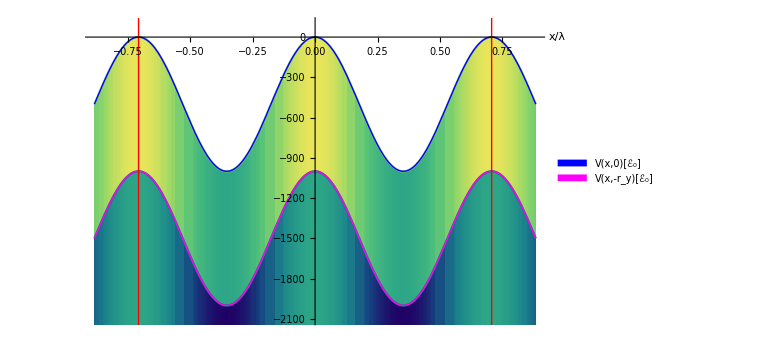

```mathematica
p2 =Show[{Plot[vscalar[nxr,y+nyr], {y,-2.5nyr,2.5nyr}, ColorFunction->cf2,Filling->Bottom,PlotRange->{-2500,100}],
Plot[vscalar[0,y+nyr], {y,-2.5nyr,2.5nyr}, ColorFunction->cf1,Filling->Bottom,PlotRange->{-2500,-1000}],
Plot[vscalar[0,y+nyr], {y,-2.5nyr,2.5nyr}, PlotStyle->{Magenta,Thick}],
Plot[vscalar[nxr,y+nyr], {y,-2.5nyr,2.5nyr}, PlotStyle->{Blue,Thick}] },
Epilog->{Inset[SwatchLegend[{Blue, Magenta},{"V(x,0)[ℰ_0]", "V(x,-r_y)[ℰ_0]"},LegendMarkerSize->13,LabelStyle->{FontSize->15}],Scaled[{0.59,0.82}],Left], 
 Red,InfiniteLine[{-2nyr,-100},{0,1}], InfiniteLine[{2nyr,-100},{0,1}]}, ImageSize->Large, PlotRange->{-2100,100},
AxesLabel->{Style["x/λ",FontSize->16],None},LabelStyle->{Black,Bold}]
```

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L4\\PER-vscalar-plaq-1D.png",p2,ImageResolution->200]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L4\PER-vscalar-plaq-1D.png

```mathematica
imdPER2 = Import["D:\\Licencjat-data\\plaqPER-dPER2.wl"];
```

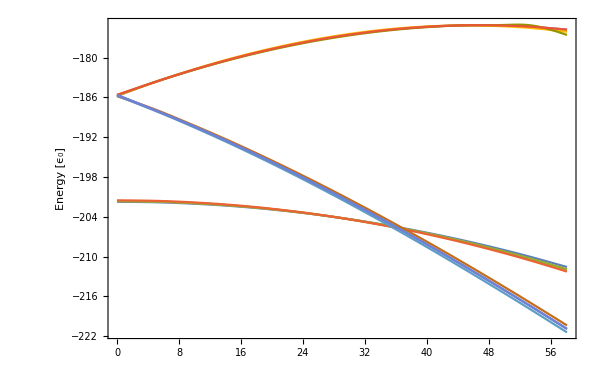

```mathematica
p3 =PlotEnergyFromSorted[imdPER2]
```

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L4\\PER-fromb-03.pdf",p3]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L4\PER-fromb-03.pdf

```mathematica
imdPER4 = Import["D:\\Licencjat-data\\plaqPER-dPER4.wl"];
```

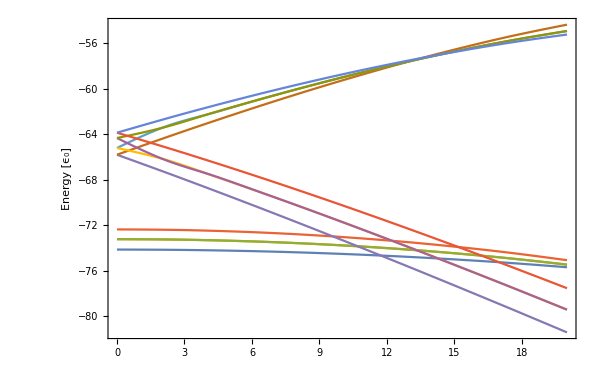

```mathematica
p4=Show[PlotEnergyFromSorted[imdPER4]]
```

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L4\\PER-fromb-02.pdf",p4]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L4\PER-fromb-02.pdf

```mathematica
dPER2 =  ParallelTable[{B, Chop[Transpose[Take[Sort[Transpose[fsol[B,0,0,0.2,2,GuessShift[B,0.2],8]]],8]]]},{B,5,40,50} ];
```

```mathematica
p5 =GraphicsColumn[Table[Show[wavePlotB[dPER2[[1,2,2,i]],i==4,i==1,i]],
{i,4,1,-1}],Spacings->-5,ImageSize->700,ImagePadding->{{0,0},{0,10}}, PlotRangePadding->None]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L4\\PER-02-podst.png",p5,ImageResolution->150]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L4\PER-02-podst.png

```mathematica
p6 =GraphicsColumn[Table[Show[wavePlotB[dPER2[[1,2,2,i]],i==8,i==5,i]],{i,8,5,-1}],Spacings->-5,ImageSize->700,ImagePadding->{{0,0},{0,10}}, PlotRangePadding->None]
```

-Graphics-

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L4\\PER-02-wzb.png",p6,ImageResolution->150]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L4\PER-02-wzb.png

```mathematica
imdPER3 = Import["D:\\Licencjat-data\\plaqPER-dPER3.wl"];
```

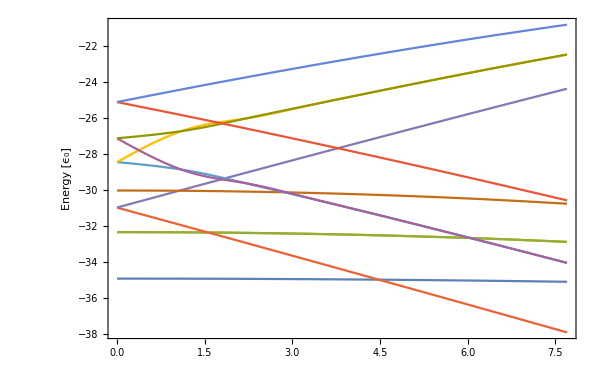

```mathematica
p7 =PlotEnergyFromSorted[imdPER3]
```

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L4\\PER-fromb-015.pdf",p7]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L4\PER-fromb-015.pdf

```mathematica
imdPER5 = Import["D:\\Licencjat-data\\plaqPER-dPER5.wl"];
```

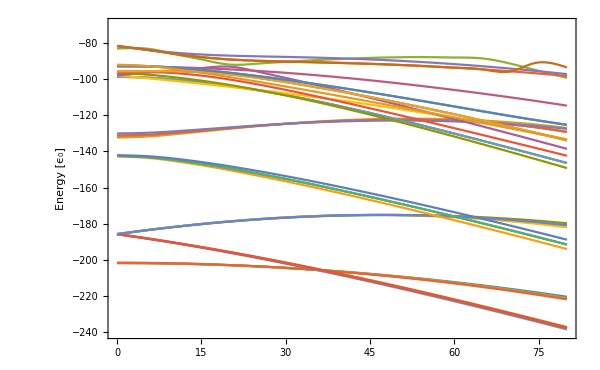

```mathematica
p8 = Show[PlotEnergyFromSorted[imdPER5],PlotRange->{-240,-70},PlotRangePadding->None]
```

```mathematica
Export["C:\\Users\\kamil\\OneDrive\\Documents\\licencjat\\latex\\earlyjpg\\L4\\PER-fromb-03-duzo.pdf",p8]
```

C:\Users\kamil\OneDrive\Documents\licencjat\latex\earlyjpg\L4\PER-fromb-03-duzo.pdf

```mathematica
dPER =  ParallelTable[{B, Chop[Transpose[Take[Sort[Transpose[fsol[B,0,0,0.3,2,GuessShift[B,0.3],6]]],6]]]},{B,30,41,5} ];
```

$Aborted

```mathematica
GraphicsColumn[Table[GraphicsRow[Transpose[wavePlot[dPER[[1,2,2,i]]]][[1]],ImageSize->1000],{i,4,1, -1}],ImageSize->600]
```

-Graphics-

```mathematica
dPER2 =  ParallelTable[{B, Chop[Transpose[Take[Sort[Transpose[fsol[B,0,0,0.2,2,GuessShift[B,0.2],8]]],8]]]},{B,5,41,50} ];
```

```mathematica
GraphicsColumn[Table[GraphicsRow[Transpose[wavePlot[dPER2[[1,2,2,i]]]][[1]],ImageSize->1000],{i,4,1,-1}],ImageSize->600]
```

-Graphics-

```mathematica
GraphicsColumn[Table[GraphicsRow[Transpose[wavePlot[dPER2[[1,2,2,i]]]][[1]],ImageSize->1000],{i,8,5,-1}],ImageSize->600]
```

-Graphics-

```mathematica
ContourPlot[vscalar[x+nxr,y+nyr], {x,-4nxr,4nxr}, {y,-4nyr,4nyr},Epilog->{Green, Thick,InfiniteLine[{0, 2nyr},{1,0}], InfiniteLine[{0, -2nyr},{1,0}], InfiniteLine[{2nxr, 0},{0,1}], InfiniteLine[{-2nxr,0},{0,1}]}]
```

-Graphics-

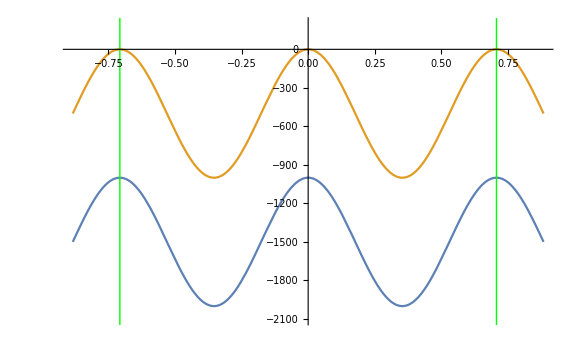

```mathematica
Plot[{vscalar[x+nxr,0],vscalar[x+nxr,nyr]}, {x,-2.5nxr,2.5nxr}, Epilog->{Green, Thick,InfiniteLine[{2nxr,vscalar[3nxr,0]},{0,1}], InfiniteLine[{-2nxr,vscalar[-nxr,0]},{0,1}]}, PlotRange->{-2100,200}, ImageSize->Large]
```

```mathematica
{xn,yn}
```

{2,2}

```mathematica
dPER2 =  sortEnergyFromWAVE@ParallelTable[{B, Chop[Transpose[Take[Sort[Transpose[fsol[B,0,0,0.3,2,GuessShift[B,0.3],12]]],12]]]},{B,0.001,60,4.15} ];
```

```mathematica
Export["D:\\Licencjat-data\\plaqPER-dPER2.wl", dPER2]
```

D:\Licencjat-data\plaqPER-dPER2.wl

D:\Licencjat-data\plaqPER-dPER2.wl

```mathematica
dPER3 =  sortEnergyFromWAVE@ParallelTable[{B, Chop[Transpose[Take[Sort[Transpose[fsol[B,0,0,0.15,2,GuessShift[B,0.15],12]]],12]]]},{B,0.001,8.2,1.1} ];
```

```mathematica
Export["D:\\Licencjat-data\\plaqPER-dPER3.wl", dPER3]
```

D:\Licencjat-data\plaqPER-dPER3.wl

```mathematica
dPER4 =  sortEnergyFromWAVE@ParallelTable[{B, Chop[Transpose[Take[Sort[Transpose[fsol[B,0,0,0.2,2,GuessShift[B,0.2],12]]],12]]]},{B,0.001,22,2} ];
```

```mathematica
Export["D:\\Licencjat-data\\plaqPER-dPER4.wl", dPER4]
```

D:\Licencjat-data\plaqPER-dPER4.wl

```mathematica
dPER5 =  sortEnergyFromWAVE@ParallelTable[{B, Chop[Transpose[Take[Sort[Transpose[fsol[B,0,0,0.3,2,GuessShift[B,0.3],36]]],36]]]},{B,0.001,81,5} ];
```

```mathematica
Export["D:\\Licencjat-data\\plaqPER-dPER5.wl", dPER5]
```

D:\Licencjat-data\plaqPER-dPER5.wl

D:\Licencjat-data\plaqPER-dPER5.wl

```mathematica
name = "D:\\Licencjat-data\\plaqPER-dPER5.wl";
temp = Import[name];
Export[name,helper@temp];
```

```mathematica
dPER6 =  Table[{B, Chop[Transpose[Take[Sort[Transpose[fsol[B,0,0,0.3,2,GuessShift[B,0.3],4]]],4]]]},{B,31,42,5} ];
```

```mathematica
Table[GraphicsColumn[Table[GraphicsRow[Transpose[wavePlot[dPER6[[j,2,2,i]]]][[1]],ImageSize->1000],{i,4,1,-1}],ImageSize->600],{j,3}]
```

{-Graphics-,-Graphics-,-Graphics-}